## 第七次作业

#### (1).

κ单位为 J/(m×s×K);
η为 Pa×s=(J×s)/m^3;
C_V 为J/(kg×K);
D 为 m^2/s.

```mathematica
(J/(m×s×K))/((J×s)/m^3*J/(kg×K))
```

(kg m^2)/(J s^2)

上式即为1.

```mathematica
(kg/m^3*m^2/s)/((J×s)/m^3)
```

(kg m^2)/(J s^2)

亦为1.

与Einstein - Stokes 关系的区别在于原式在稀薄气体中成立，而Einstein - Stokes 关系是在液体中成立。由于是在液体中，分子的直径在扩散过程中更为明显，所以Einstein - Stokes关系中出现了r，粘滞效果也更为明显，因此是阻止扩散；而稀薄气体分子直径影响小，粘滞效果反而促进了扩散，这可能是由于在这个情况下分子之间的粘滞使得分子容易被“带出来”。

#### (2).

```mathematica
f[x_,t_]:=Exp[-x^2/(4*d*t)]/Sqrt[4Pi*d*t];
d*D[D[f[x,t],x],x]-D[f[x,t],t]
```

(d ⅇ^(-x^2/(4 d t)))/(4 √π (d t)^(3/2))-(ⅇ^(-x^2/(4 d t)) x^2)/(8 d √π t^2 √(d t))+d (-(ⅇ^(-x^2/(4 d t)))/(4 d √π t √(d t))+(ⅇ^(-x^2/(4 d t)) x^2)/(8 d^2 √π t^2 √(d t)))

```mathematica
Simplify@%
```

0

故满足一维扩散方程。

```mathematica
Integrate[f[x,t],{x,-Infinity,Infinity}]
```

ConditionalExpression[√(1/(d t)) √(d t),Re[1/(d t)]>0]

```mathematica
Limit[f[0,t],t->0]
```

DirectedInfinity[1/(√Sign[d])]

可得x=0时f[x,t]在t -> 0 时值趋近于无穷大，而由于在实数域上的积分为1，故在x≠0时其值为零。从而其为x=0的Dirac δ函数，其表明了分子只可能在原点上，而由于整个空间上概率必定满足1。

```mathematica
Integrate[x^2 f[x,t],{x,-Infinity,Infinity}]
```

ConditionalExpression[2 √(1/(d t)) (d t)^(3/2),Re[1/(d t)]>0]

得证。

#### (3).

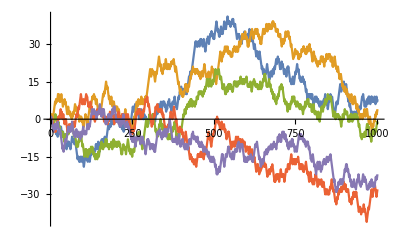

```mathematica
list1D:=FoldList[Plus,0,Table[RandomChoice[{-1,1}],1000]];
ListLinePlot[Table[list1D,5]]
```

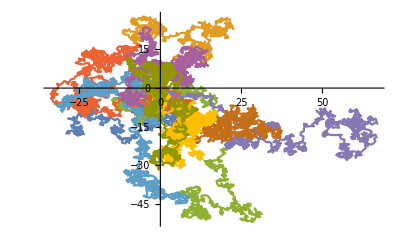

```mathematica
list2D:=FoldList[Plus,{0,0},Table[({Cos@#,Sin@#}&@RandomReal[{0,2Pi}]),1000]]
ListLinePlot[Table[list2D,10]]
```

```mathematica
list3D:=FoldList[Plus,{0,0,0},Table[({Cos[#1]*Cos[#2],Sin[#1]*Cos[#2],Sin[#2]}&[RandomReal[{0,2Pi}],RandomReal[{-Pi/2,Pi/2}]]),1000]]
ListPointPlot3D[Table[list3D,5],BoxRatios->{1, 1, 1}]
```

-Graphics3D-

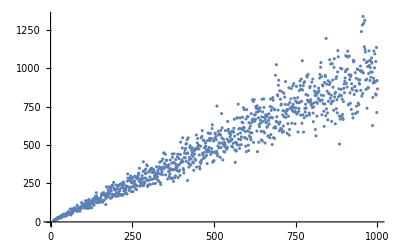

```mathematica
MSD[steps_]:=Total[Table[RandomChoice[{-1,1}],steps]];
ListPlot@Table[{steps,Total[#^2&/@Table[MSD[steps],100]]/100},{steps,10,1000,1}]
```

得到了充分的证明。

#### (4).

由于模拟分布函数需要通过更多的算法，因此会相较平均生成随机数而言需要更多的时间生成随机数；而模拟的时候有很多的因素需要考虑，因此在模拟的时候是高维度模拟，此时仍旧使用模拟分布函数的方法会非常的低效。（但我个人觉得像mathematica这样对基础算法进行过优化的软件可能改变这样的情况，如下面）

```mathematica
AbsoluteTiming[RandomVariate[NormalDistribution[]]]
```

{0.000038,-0.372174}

```mathematica
AbsoluteTiming[RandomReal[]]
```

{5.×10^-6,0.748987}

两者所耗时间相差约10。虽然的确10已经是不小的数字了，但如果追求精确性的话或许模拟分布函数也不再是不可行的方法（特别是现在硬件水平越来越高的情况下）

它们二者之间有着共同的思想，便是这个时刻的位置／分布是由上一个时刻的位置／分布所决定的，每个元素在一个固定时刻只能发生固定路径长度、方向任意的位移。在系综中最后求的是最终与时间无关的函数，而时间轨迹平均方法是为了得到非平衡态变化过程。

#### (5).

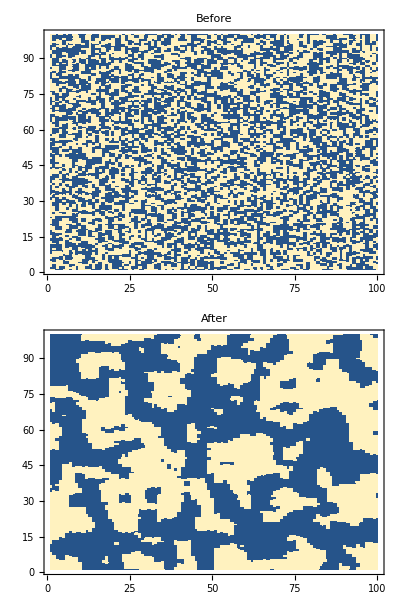

```mathematica
IsingPlot[length_,J_,T_,Recursiondepth_]:=Module[{A,before,after,position,ΔH,Manipulation},

Evaluate[(Flatten@Table[A[i,j],{i,0,length+1},{j,0,length+1}])]=Evaluate[Flatten@(PadLeft[PadRight[Table[RandomChoice[{1,1}->{-1,1}],{i,length},{j,length}],{length+1,length+1}],{length+2,length+2}])];
position:={RandomChoice@Range@length,RandomChoice@Range@length};
before=ListDensityPlot[Flatten[Table[{i,j,A[i,j]},{i,length},{j,length}],1],InterpolationOrder->0,PlotLabel->"Before"];
ΔH[position_]:=Total[-2*J*(A@@(position+#))*(A@@position)&/@{{0,1},{1,0},{-1,0},{0,-1}}];

Manipulation[a_,b_]:=If[ΔH[{a,b}]<0,A[a,b]=-1*A[a,b],If[Evaluate[RandomReal[{0,1}]]<Exp[-ΔH[{a,b}]/T],A[a,b]=-1*A[a,b]]];
Do[Manipulation@@position,Recursiondepth];
after=ListDensityPlot[Flatten[Table[{i,j,A[i,j]},{i,length},{j,length}],1],InterpolationOrder->0,PlotLabel->"After"];
Column[{before,after}]
];
(*length代表Ising 模型的边长，Recursiondepth表示判断方向翻转的次数*)
IsingPlot[100,-100,100,100000]
```

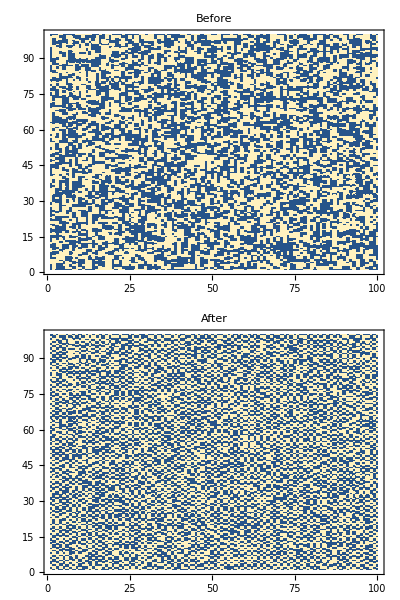

```mathematica
IsingPlot[100,100,100,100000]
```

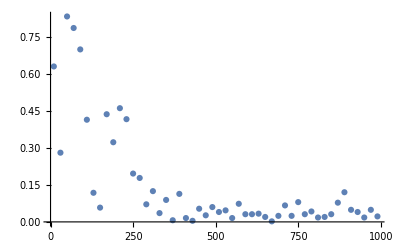

```mathematica
IsingM[length_,J_,T_,Recursiondepth_]:=Module[{A,after,position,ΔH,Manipulation},Evaluate[(Flatten@Table[A[i,j],{i,0,length+1},{j,0,length+1}])]=Evaluate[Flatten@(PadLeft[PadRight[Table[RandomChoice[{1,1}->{-1,1}],{i,length},{j,length}],{length+1,length+1}],{length+2,length+2}])];
position:={RandomChoice@Range@length,RandomChoice@Range@length};
ΔH[position_]:=Total[-2*J*(A@@(position+#))*(A@@position)&/@{{0,1},{1,0},{-1,0},{0,-1}}];

Manipulation[a_,b_]:=If[ΔH[{a,b}]<0,A[a,b]=-1*A[a,b],If[Evaluate[RandomReal[{0,1}]]<Exp[-ΔH[{a,b}]/T],A[a,b]=-1*A[a,b]]];
Do[Manipulation@@position,Recursiondepth];
after=Abs@@((Flatten@Take[Total[Flatten[Table[{i,j,A[i,j]},{i,length},{j,length}],1]],-1])/(length^2))
]
list=Table[{i,IsingM[30,-100,i,100000]},{i,Table[k,{k,10,1000,20}]}];
ListPlot[Abs/@Flatten/@list]
```

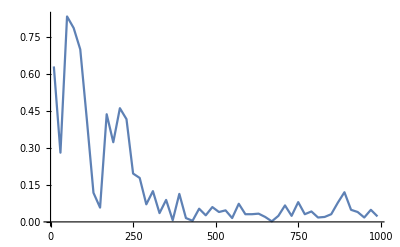

```mathematica
ListLinePlot[Abs/@Flatten/@list]
```

可以看到，在较低温度下模型具有较高的磁矩，从而体现为铁磁性，而在较高温下磁矩较小，表现为顺磁性。大致可以看出该模拟相变温度为200～300间。

```mathematica
list(*上面的代码运行所耗时间非常有毒，所以这里暂存了数据*)
```

{{10,283/450},{30,7/25},{50,187/225},{70,353/450},{90,157/225},{110,31/75},{130,53/450},{150,13/225},{170,98/225},{190,29/90},{210,23/50},{230,187/450},{250,44/225},{270,8/45},{290,16/225},{310,28/225},{330,8/225},{350,4/45},{370,1/150},{390,17/150},{410,7/450},{430,1/225},{450,4/75},{470,2/75},{490,3/50},{510,1/25},{530,7/150},{550,7/450},{570,11/150},{590,7/225},{610,7/225},{630,1/30},{650,1/50},{670,1/450},{690,11/450},{710,1/15},{730,11/450},{750,2/25},{770,7/225},{790,19/450},{810,4/225},{830,1/50},{850,7/225},{870,7/90},{890,3/25},{910,11/225},{930,1/25},{950,4/225},{970,11/225},{990,1/45}}